assume that the two materials have the same radial dielectric function ϵr  but that one of them has a different vertical dielectric function ϵz

## Charge q in the uniform dielectric at distance a along the z axis from from a non-uniform dielectric

```mathematica
Vu1= q/(ϵr √((z-a)^2+r^2))+q (ϵr- √(ϵr ϵz))/(ϵr + √(ϵr ϵz))1/(ϵr √((z+a)^2+r^2))
Vb1 = (2 q)/(√(ϵr ϵz)+ ϵr)1/(√(r^2+(z √(ϵr/ϵz)-a)^2))
```

q/(√(r^2+(-a+z)^2) ϵr)+(q (ϵr-√(ϵr ϵz)))/(√(r^2+(a+z)^2) ϵr (ϵr+√(ϵr ϵz)))

(2 q)/(√(r^2+(-a+z √(ϵr/ϵz))^2) (ϵr+√(ϵr ϵz)))

```mathematica
FullSimplify[(Vu1/. {z->0})]
FullSimplify[(Vb1/. {z->0})]
```

(2 q)/(√(a^2+r^2) (ϵr+√(ϵr ϵz)))

(2 q)/(√(a^2+r^2) (ϵr+√(ϵr ϵz)))

## Charge q in the non-uniform dielectric at distance a along the z axis from from a uniform dielectric

```mathematica
Vu2 = (2 q)/(ϵr +√(ϵz ϵr))1/(√(r^2+((z+a) √(ϵr/ϵz))^2))
Vb2= q/(√(ϵz ϵr))(1/(√(r^2+((z+a) √(ϵr/ϵz))^2))+((√(ϵr ϵz)-ϵr)/(√(ϵr ϵz) + ϵr))1/(√(r^2+((z-a) √(ϵr/ϵz))^2)))
```

(2 q)/(√(r^2+((a+z)^2 ϵr)/ϵz) (ϵr+√(ϵr ϵz)))

(q (1/(√(r^2+((a+z)^2 ϵr)/ϵz))+(-ϵr+√(ϵr ϵz))/(√(r^2+((-a+z)^2 ϵr)/ϵz) (ϵr+√(ϵr ϵz)))))/(√(ϵr ϵz))

```mathematica
FullSimplify[(Vu2/. {z->0})]
FullSimplify[(Vb2/. {z->0})]
```

(2 q)/(√(r^2+(a^2 ϵr)/ϵz) (ϵr+√(ϵr ϵz)))

(2 q)/(√(r^2+(a^2 ϵr)/ϵz) (ϵr+√(ϵr ϵz)))

## Putting it together:

z1, r1 are  the coordinates in distances radially and azimuthally from the charge in the uniform dielectric.

```mathematica
V[ϵr_, ϵz_, r1_,r2_,z1_,z2_] :=  (ϵr- √(ϵr ϵz))/(ϵr + √(ϵr ϵz))1/(ϵr √((2z1)^2))-1/2 2/(√(ϵr ϵz)+ ϵr)1/(√((r1+r2)^2+(z1 √(ϵr/ϵz)+z2)^2))-
1/2 2/(ϵr +√(ϵz ϵr))1/(√((r1+r2)^2+((z1+z2) √(ϵr/ϵz))^2))
```

```mathematica
Tmp1[z_] := FullSimplify[V[4/(27.21*0.529) , 1.5/(27.21*0.529), 0,0, z, 5]] 
Tmp1[15]
Tmp1[5]
```

-0.115166

-0.219686

```mathematica
V[4/(27.21*0.529), 4/(27.21*0.529), 0,28.284271247461902,5,5] - 0.001 10
```

-0.129951

```mathematica
(ϵr- √(ϵr ϵz))/(ϵr + √(ϵr ϵz))/. { ϵr-> 4/(27.21*0.529)
```

```mathematica
4/(27.21*0.529)
```

0.277892

```mathematica
Tmp1[z_] := FullSimplify[V[4/(27.21*0.529) , 1/(27.21*0.529), 0,0, z, 5]] - 0.001 (z+5)
Tmp2[z_] := FullSimplify[V[4/(27.21*0.529) , 4/(27.21*0.529), 0,0, z, 5]] - 0.001 (z+5)
```

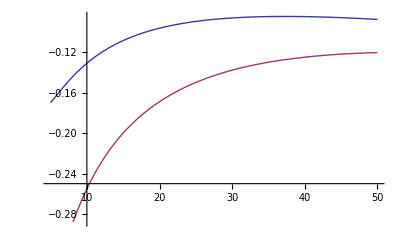

```mathematica
Plot[{Tmp1[z],Tmp2[z]}, {z, 5,50}]
```

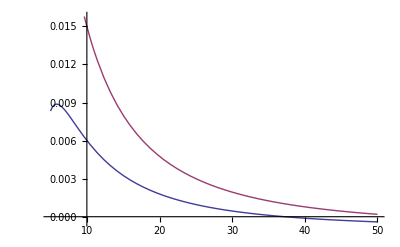

```mathematica
Plot[{(D[Tmp1[x],x]/.x->z),(D[Tmp2[x],x]/.x->z)}, {z, 5,50}]
```

```mathematica
allpot= FullSimplify[V[5/(27.21*0.529) , 1/(27.21*0.529), r,0, z, 5]]-0.001 (z+5)
allpot2= FullSimplify[V[4/(27.21*0.529) , 4/(27.21*0.529), r,0, z, 5]]-0.001 (z+5)
```

0.549805/(√(z^2))-0.001 (5+z)-1.98921/(√(r^2+5. (5+z)^2))-1.98921/(√(r^2+(5+2.23607 z)^2))

(0. √(z^2))/z^2-0.001 (5+z)-3.59852/(√(r^2+1. (5.+z)^2))

```mathematica
Plot3D[{(D[allpot,z] /.z-> h),(D[allpot2,z] /.z-> h)}, {h,5,50}, {r,0,50}, PlotRange-> All]
```

-Graphics3D-

```mathematica
NSolve[(D[FullSimplify[V[4.5/(27.21*0.529) , 1/(27.21*0.529), 0,0, z, 5]]-0.001 (z+5),z]/. z->h) == 0,h]
```

{{h→-5.06354+38.5857 ⅈ},{h→-5.06354-38.5857 ⅈ},{h→33.0355},{h→3.85925},{h→-3.65487},{h→-0.745605+1.16434 ⅈ},{h→-0.745605-1.16434 ⅈ}}

```mathematica
NSolve[(D[FullSimplify[V[4/(27.21*0.529) , 4/(27.21*0.529), 0,0, z, 5]]-0.001(z+5),z]/. z->h) == 0,h]
```

{{h→54.9877}}

```mathematica
FullSimplify[V[ϵ, ϵ, r1,r2,z1,z2] ]
```

-2/(√((r1+r2)^2+(z1+z2)^2) (ϵ+√(ϵ^2)))